# Mecanismo 13: Mecanismo de palancas articuladas para regular la longitud del punto de una máquina de coser.

## Datos

```mathematica
(*Faltan agregar todos los valores de longitudes de eslabones*)
escala = 0.126;
r0 = 1.29 * escala;(*constante*)
θ0 = 188*Degree;(*Constante*)
r1 = 0.08 * escala;
(*Cambia según el movimiento que se quiera*)
r2 = 0.08* escala;
r3 = 1.26* escala;
r4 = 0.68 * escala;
r5 = 0.41* escala;
r5p = 0.39* escala;
r6 = 1.17* escala;
```

## Ecuaciones cinemáticas

```mathematica
Clear[θ2, θ3, θ4, θ5,θ6];
Clear[ω1,ω3,ω4, ω5, ω6];
Clear[α1,α3,α4, α5, α6];
```

### Ecuaciones de posición

```mathematica
u0 ={Cos[θ0],Sin[θ0],0};
u1 = {Cos[θ2+ Pi],Sin[θ2 +Pi], 0};
u2 = {Cos[θ2], Sin[θ2],0};
u3 = {Cos[θ3], Sin[θ3],0};
u4 = {Cos[θ4], Sin[θ4],0};
u5={Cos[θ5], Sin[θ5],0};
u6 = {Cos[θ6], Sin[θ6],0};
```

```mathematica
R0 = r0 * u0;
R1 = r1 * u1;
R2 = r2*u2;
R3=r3 * u3;
R4 = r4 *u4;          
R5= r5* u5;
R5p = r5p* u5;
R6 = r6 * u6;
```

```mathematica
(*Lazos vectoriales*)
pos1 = R2 +R3-R5 - R0;
pos2 = R1+ R4 + R6 - R5p -R3 -R2;


pos1 // MatrixForm
pos2 // MatrixForm
```

(0.160958+0.01008 Cos[θ2]+0.15876 Cos[θ3]-0.05166 Cos[θ5]
0.0226212+0.01008 Sin[θ2]+0.15876 Sin[θ3]-0.05166 Sin[θ5]
0.)

(-0.02016 Cos[θ2]-0.15876 Cos[θ3]+0.08568 Cos[θ4]-0.04914 Cos[θ5]+0.14742 Cos[θ6]
-0.02016 Sin[θ2]-0.15876 Sin[θ3]+0.08568 Sin[θ4]-0.04914 Sin[θ5]+0.14742 Sin[θ6]
0.)

### Ecuaciones de velocidad

```mathematica
omega2 = {0,0,ω2};
omega3= {0,0,ω3};
omega4 = {0,0,ω4};
omega5= {0,0,ω5};
omega6= {0,0,ω6};
```

```mathematica
V1 = omega2 ×R1;
V2 = omega2×R2;
V3 = omega3 × R3;
V4 = omega4 ×R4;
V5 = omega5 ×R5;
V5p = omega5 ×R5p;
V6 = omega6 ×R6;
```

```mathematica
vel1 =V2 +V3-V5 ;
vel2= V1+ V4 + V6 - V5p -V3 -V2;

vel1 // MatrixForm
vel2//  MatrixForm
```

(0.-0.01008 ω2 Sin[θ2]-0.15876 ω3 Sin[θ3]+0.05166 ω5 Sin[θ5]
0.+0.01008 ω2 Cos[θ2]+0.15876 ω3 Cos[θ3]-0.05166 ω5 Cos[θ5]
0.)

(0.+0.02016 ω2 Sin[θ2]+0.15876 ω3 Sin[θ3]-0.08568 ω4 Sin[θ4]+0.04914 ω5 Sin[θ5]-0.14742 ω6 Sin[θ6]
0.-0.02016 ω2 Cos[θ2]-0.15876 ω3 Cos[θ3]+0.08568 ω4 Cos[θ4]-0.04914 ω5 Cos[θ5]+0.14742 ω6 Cos[θ6]
0.)

### Ecuaciones de aceleración

```mathematica
alfa2 = {0,0,α2};
alfa3 = {0,0,α3};
alfa4 = {0,0,α4};
alfa5 = {0,0,α5};
alfa6= {0,0,α6};

A0 = {0,0,0};
A1 = alfa2×R1 + ω2^2 * R1;
A2 = alfa2×R2 + ω2^2 * R2;
A3 = alfa3×R3 + ω3^2 * R3;
A4 = alfa4×R4 + ω4^2 * R4;
A5= alfa5×R5 + ω5^2 * R5;
A5p = alfa5×R5p+ ω5^2 * R5p;
A6= alfa6×R6 + ω6^2 * R6;
```

```mathematica
acel1 = A2 +A3-A5 - A0;
acel2 = A1+ A4 + A6 - A5p -A3 -A2;

acel1// MatrixForm
acel2 // MatrixForm
```

(0.+0.01008 ω2^2 Cos[θ2]+0.15876 ω3^2 Cos[θ3]-0.05166 ω5^2 Cos[θ5]-0.01008 α2 Sin[θ2]-0.15876 α3 Sin[θ3]+0.05166 α5 Sin[θ5]
0.+0.01008 α2 Cos[θ2]+0.15876 α3 Cos[θ3]-0.05166 α5 Cos[θ5]+0.01008 ω2^2 Sin[θ2]+0.15876 ω3^2 Sin[θ3]-0.05166 ω5^2 Sin[θ5]
0.)

(0.-0.02016 ω2^2 Cos[θ2]-0.15876 ω3^2 Cos[θ3]+0.08568 ω4^2 Cos[θ4]-0.04914 ω5^2 Cos[θ5]+0.14742 ω6^2 Cos[θ6]+0.02016 α2 Sin[θ2]+0.15876 α3 Sin[θ3]-0.08568 α4 Sin[θ4]+0.04914 α5 Sin[θ5]-0.14742 α6 Sin[θ6]
0.-0.02016 α2 Cos[θ2]-0.15876 α3 Cos[θ3]+0.08568 α4 Cos[θ4]-0.04914 α5 Cos[θ5]+0.14742 α6 Cos[θ6]-0.02016 ω2^2 Sin[θ2]-0.15876 ω3^2 Sin[θ3]+0.08568 ω4^2 Sin[θ4]-0.04914 ω5^2 Sin[θ5]+0.14742 ω6^2 Sin[θ6]
0.)

### Solución inicial

```mathematica
Clear[θ2, θ3,θ4, θ5,θ6];
θ2 = 59 * Degree;(*Variable de control, ángulo de posisción inicial*)
SolInicial = FindRoot[{
pos1[[1]] == 0,
pos1[[2]] ==0,
pos2[[1]]==0,
pos2[[2]] ==0},
{{θ3, (*Valor semilla*) 170* Degree},
{θ4, (*Valor semilla*) 80* Degree},
{θ5,(*Valor semilla*) 80* Degree},
{θ6, (*Valor semilla*)180* Degree}}, MaxIterations->30]

(θ3/.SolInicial)/Degree
(θ4 /.SolInicial)/Degree
(θ5/.SolInicial)/Degree
(θ6/.SolInicial)/Degree
```

{θ3→3.01734,θ4→1.47189,θ5→1.40328,θ6→3.1406}

172.881

84.3331

80.4018

179.943

### Solución total

```mathematica
Clear[θ2, θ3,θ4, θ5,θ6];
θ3i=θ3/.SolInicial;
θ4i=θ4/.SolInicial;
θ5i=θ5/.SolInicial;
θ6i=θ6/.SolInicial;

For[i = 59 , i ≤ 419, i+=1,
θ2 = i*Degree;
SolPos[i] = FindRoot[{
pos1[[1]] == 0,
pos1[[2]] ==0,
pos2[[1]]==0,
pos2[[2]] ==0},
{{θ3, θ3i},
{θ4, θ4i},
{θ5,θ5i},
{θ6, θ6i}}, MaxIterations->300];

θ3i=θ3/.SolPos[i];
θ4i=θ4/.SolPos[i];
θ5i=θ5/.SolPos[i];
θ6i=θ6/.SolPos[i];];
```

## Gráficas de posición

```mathematica
tabla1=Table[{i,(θ3/.SolPos[i])/Degree},{i,59,419,1}];
tabla2=Table[{i,(θ4/.SolPos[i])/Degree},{i,59,419,1}];
tabla3=Table[{i,(θ5/.SolPos[i])/Degree},{i,59,419,1}];
tabla4=Table[{i,(θ6/.SolPos[i])/Degree},{i,59,419,1}];
```

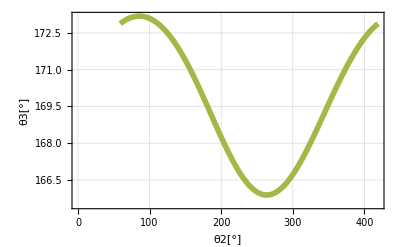

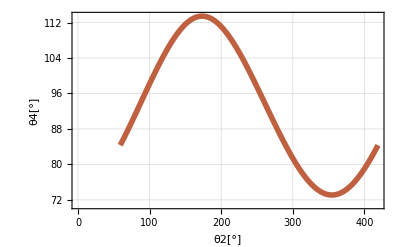

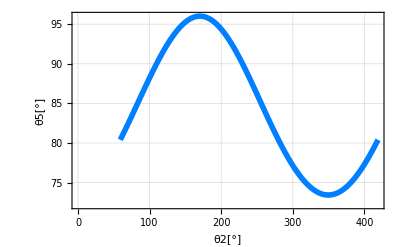

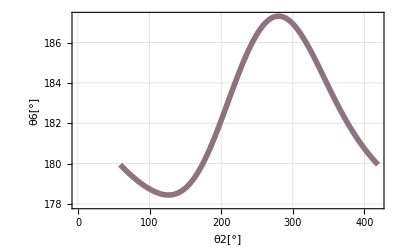

```mathematica
ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ2[°]","θ3[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{RGBColor[0.635294, 0.721569, 0.278431],Thickness[.01]},
ImageSize->400]

ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ2[°]","θ4[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{RGBColor[0.74902, 0.376471, 0.25098],Thickness[.01]},
ImageSize->400]


ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ2[°]","θ5[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{RGBColor[0, 0.501961, 1],Thickness[.01]},
ImageSize->400]

ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ2[°]","θ6[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{RGBColor[0.552941, 0.447059, 0.505882],Thickness[.01]},
ImageSize->400]
```

## Solución de velocidad

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];

ω2=50;

For[i=59,i≤419,i+=1,
θ2=i*Degree;
SolVel[i]=Solve[{        
vel1[[1]]==0,
vel1[[2]]==0,
vel2[[1]]==0,
vel2[[2]]==0}/.SolPos[i],      
{ω3,ω4,ω5,ω6}]//Flatten ]
?SolVel;
```

Missing[UnknownSymbol,SolVel;]

## Gráficas de velocidad

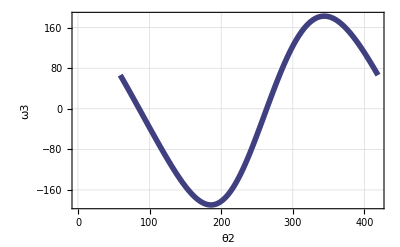

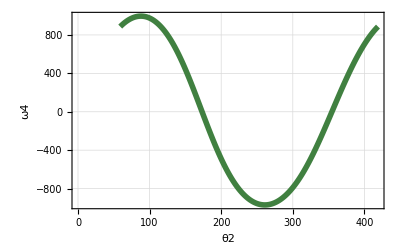

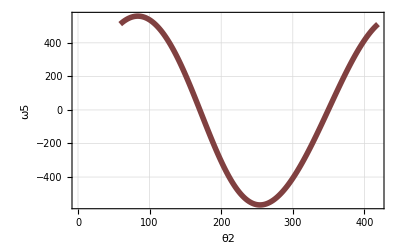

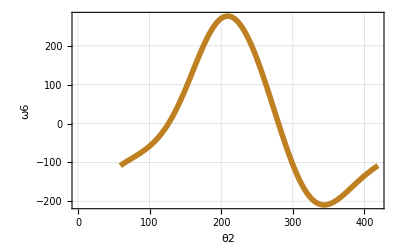

```mathematica
tabla1=Table[{i,(ω3/.SolVel[i])/Degree},{i,59,419,1}];
tabla2=Table[{i,(ω4/.SolVel[i])/Degree},{i,59,419,1}];
tabla3=Table[{i,(ω5/.SolVel[i])/Degree},{i,59,419,1}];
tabla4=Table[{i,(ω6/.SolVel[i])/Degree},{i,59,419,1}];


ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ2","ω3"},
Joined->True,
PlotStyle->{RGBColor[0.25,0.25,0.5],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ2","ω4"},
Joined->True,
PlotStyle->{RGBColor[0.25,0.5,0.25],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ2","ω5"},
Joined->True,
PlotStyle->{RGBColor[0.5,0.25,0.25],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ2","ω6"},
Joined->True,
PlotStyle->{RGBColor[0.75,0.5,0.13],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]
```

## solución de aceleración

```mathematica
Clear[α2,α3,α4,α5,α6];
α2 = 0;
```

```mathematica
For[i=59,i≤419,i+=1, 
θ2=i*Degree;  

SolAcel[i]=Solve[{
acel1[[1]]==0,
acel1[[2]]==0,
acel2[[1]]==0,
acel2[[2]]==0}/.SolPos[i]/.SolVel[i],
{α3,α4,α5,α6}]//Flatten]
```

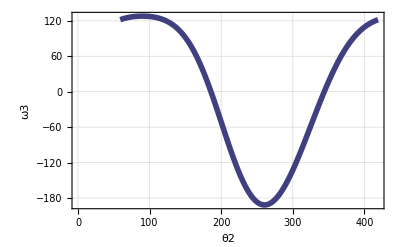

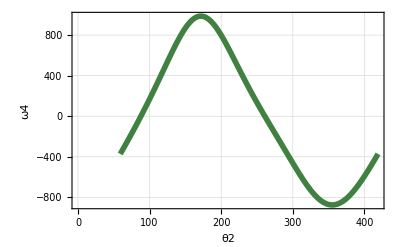

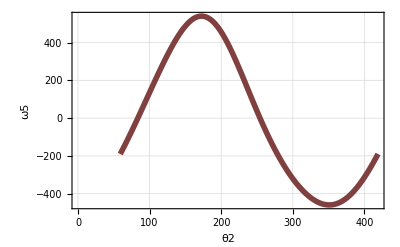

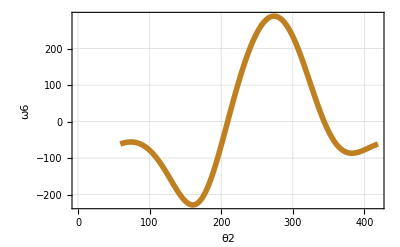

```mathematica
tabla1=Table[{i,α3/.SolAcel[i]},{i,59,419,1}];
tabla2=Table[{i,α4/.SolAcel[i]},{i,59,419,1}];
tabla3=Table[{i,α5/.SolAcel[i]},{i,59,419,1}];
tabla4=Table[{i,α6/.SolAcel[i]},{i,59,419,1}];
ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ2","ω3"},
Joined->True,
PlotStyle->{RGBColor[0.25,0.25,0.5],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ2","ω4"},
Joined->True,
PlotStyle->{RGBColor[0.25,0.5,0.25],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ2","ω5"},
Joined->True,
PlotStyle->{RGBColor[0.5,0.25,0.25],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ2","ω6"},
Joined->True,
PlotStyle->{RGBColor[0.75,0.5,0.13],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]
```